#### Data thief existing constraints of Q vs. m_s (lines on log-log scale)

```mathematica
OA1={{1.9882697947214076,34.76014760147601},
{2.8592375366568916,33.726937269372684}};
OA2={{2.8592375366568916,33.726937269372684},{
2.348973607038123,31.586715867158667}};
TA1={{2.348973607038123,31.586715867158667},{
3.736070381231672,29.815498154981544}};
TA2={{3.736070381231672,29.815498154981544},{
1.9882697947214076,22.50922509225092}};
SuperK={{1.9912023460410557,25.461254612546117},{
4.69208211143695,21.992619926199257}};
Stability={{1.9882697947214076,10.84870848708487},{
5.011730205278592,23.025830258302577}};
```

```mathematica
OA1plot=Plot[Interpolation[OA1,InterpolationOrder->1][x],{x,1,2.8592375366568916},PlotStyle->{Red}];
OA2plot=Plot[Interpolation[OA2,InterpolationOrder->1][x],{x,2.348973607038123,2.8592375366568916},PlotStyle->{Red}];
TA1plot=Plot[Interpolation[TA1,InterpolationOrder->1][x],{x,2.348973607038123,3.736070381231672},PlotStyle->{Red}];
TA2plot=Plot[Interpolation[TA2,InterpolationOrder->1][x],{x,2.5,3.736070381231672},PlotStyle->{Red}];
SuperKplot=Plot[Interpolation[SuperK,InterpolationOrder->1][x],{x,2.5,4.8},PlotStyle->{Red}];
Stabilityplot=Plot[Interpolation[Stability,InterpolationOrder->1][x],{x,1,8},PlotStyle->{Red,Dashed}];
```

InterpolatingFunction::dmval: Input value {1.00004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00014} lies outside the range of data in the interpolating function. Extrapolation will be used.

#### Our limits

```mathematica
Qballboom[x_]:=41.80158027195581+ 4(x-3)
QballNuStar[x_]:=59.54572245905269-4/3(x-3)
QballRX[x_]:=55.01513578082331-4/3(x-3)
Qballgravity[x_]:=52.93196000578135-4/3(x-3)
Qballtrigger[x_]:=48+4(x-3)
QballBH[x_]:=64-4(x-3)
boom=Plot[Qballboom[x],{x,1,8},PlotStyle->{Purple}];
friction=Plot[Qballgravity[x],{x,1,8},PlotStyle->{Cyan}];
trigger=Plot[Qballtrigger[x],{x,1,8},PlotStyle->{Magenta}];
NuStar=Plot[QballNuStar[x],{x,1,8},PlotStyle->{Gray}];
RX=Plot[QballRX[x],{x,1,8},PlotStyle->{Blue}];
BH=Plot[QballBH[x],{x,1,8},PlotStyle->{Black}];
excludedRX=RegionPlot[{y≥Qballboom[x]&& y≤Min[QballRX[x],QballBH[x]]},{x,1,8},{y,10,70}];
excludedNuStar=RegionPlot[{y≥Qballboom[x]&& y≤Min[QballNuStar[x],QballBH[x]]},{x,1,8},{y,10,70},PlotStyle->{LightGray}];
XLabelQ={{2,"10^2"},{3,"10^3"},{4,"10^4"},{5,"10^5"},{6,"10^6"},{7,"10^7"}};
YLabelQ={{10,"10^10"},{20,"10^20"},{30,"10^30"},{40,"10^40"},{50,"10^50"},{60,"10^60"},{70,"10^70"}};
canvasQball=Plot[-1,{x,2,7},PlotRange->{21,68},Frame->True,FrameTicks->{{YLabelQ,None},{XLabelQ,None}},FrameStyle->Black,FrameLabel->{"m_S (GeV)","Q"},LabelStyle-> Directive[Bold]];
```

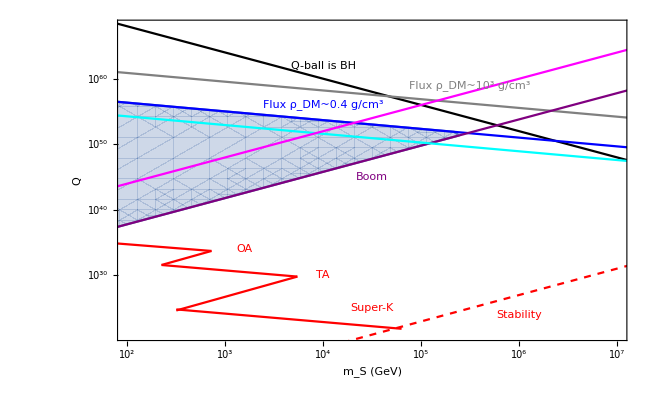

```mathematica
Show[canvasQball,OA1plot,OA2plot,TA1plot,TA2plot,SuperKplot,Stabilityplot,excludedRX,BH,NuStar,RX,boom,friction,trigger,Graphics[Inset[Style["OA",Small,Red,FontFamily->"Helvetica"],{3.2,34},{0,0},1,{1,0}]],Graphics[Inset[Style["TA",Small,Red,FontFamily->"Helvetica"],{4,30},{0,0},1,{1,0}]],Graphics[Inset[Style["Super-K",Small,Red,FontFamily->"Helvetica"],{4.5,25},{0,0},1,{1,0}]],Graphics[Inset[Style["Stability",Small,Red,FontFamily->"Helvetica"],{6,24},{0,0},2,{1,1/5}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{4.5,45},{0,0},2,{1,1/4}]],Graphics[Inset[Style["Q-ball is BH",Small,Black,FontFamily->"Helvetica"],{4,62},{0,0},2,{1,-1/4}]],Graphics[Inset[Style["Flux ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{4,56},{0,0},2,{1,-1/12.5}]],Graphics[Inset[Style["Flux ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{5.5,59},{0,0},2,{1,-1/12.5}]],ImageSize->Medium]
```

```mathematica
Solve[10^4/((10^19)^2)ms Q^(3/4)==10^-5 *(0.2 *10^-13)^-1,Q]
```

{{Q→8.54988×10^56 (1/ms)^(4/3)}}

```mathematica
Log10[8.549879733383481*^56 (10.^-ms)^(4/3)]/.ms->3
```

52.932

```mathematica
52.93196000578135-4/3(x-3)
```

```mathematica
Solve[Q^(1/4)/10^ms*0.2 10^-13 ==10^-5,Q]
```

{{Q→6.25×10^34 10.^(4. ms)}}

```mathematica
Log10[6.249999999999996*^34 10.^(4. ms)]/.ms->3
```

46.7959